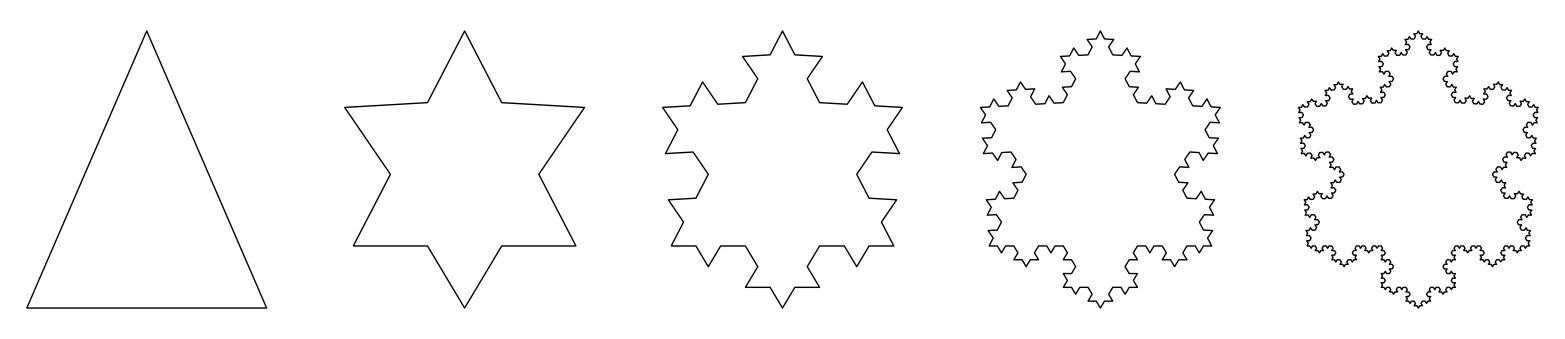

```mathematica
(* Raquel Lippincott - 2017
	Mathematica Notebook *)

Koch[a_, b_, currIt_,exitIt_] := 
If [currIt <= exitIt, {
Module[{a1, b1, distance, heading, c, k1, k2, k3, k4},
	a1 = 2*a/3 + b/3;
	b1 = 2*b/3 + a/3;
	distance  =EuclideanDistance[a,b]/3;
	heading = ArcTan[(b[[2]]-a[[2]])/(b[[1]]-a[[1]])];
	If[b[[1]]<a[[1]],
	heading += Pi;
	];
	c = a1 + distance*{Cos[heading + Pi/3], Sin[heading + Pi/3]};
	k1 = Koch[a, a1, currIt+1, exitIt];
	k2 = Koch[a1, c, currIt+1, exitIt];
	k3 = Koch[c, b1, currIt+1, exitIt];
	k4 = Koch[b1, b, currIt+1, exitIt];
	Join[k1,k2,k3,k4]]
},{
{a,b}
}]

KochSnowflake[iterations_]:=
Module[{k1, k2, k3},
k1 = Flatten[Koch[{0,0},{1,2},1,iterations]];
k2 = Flatten[Koch[{1,2},{2,0},1,iterations]];
k3 = Flatten[Koch[{2,0},{0,0},1,iterations]];
Partition[Flatten[Join[k1, k2, k3]],2]
]

KochCurvePlot[iterations_]:=
GraphicsGrid[{Table[Graphics[Line[KochSnowflake[i]]],{i,0,iterations-1}]}, ImageSize->Full]

KochCurvePlot[5]
```